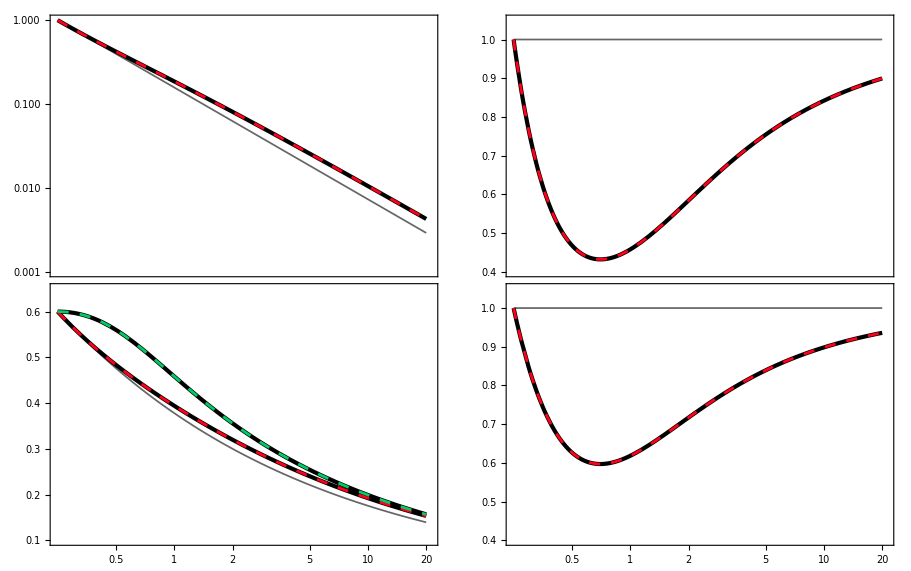
-Graphics-τ (fm/c)

/Users/Michael/Desktop/cpu_vah/mathematica/bjorken_test/bjorken_plot.pdf

```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];

(* CPU VAH *)
eVAH=Interpolation[Take[Import[wd<>"/../../output/eratio.dat"]]];
plptratioVAH=Interpolation[Take[Import[wd<>"/../../output/plptratio.dat"]]];
TVAH=Interpolation[Take[Import[wd<>"/../../output/T.dat"]]];
LambdaVAH=Interpolation[Take[Import[wd<>"/../../output/Lambda.dat"]]];
aLVAH=Interpolation[Take[Import[wd<>"/../../output/aL.dat"]]];

(* Conformal Bjorken *)
eBjorken=Interpolation[Take[Import[wd<>"/bjorken_data/eplot_conformal_vah.dat"]]];
plptBjorken=Interpolation[Take[Import[wd<>"/bjorken_data/plptplot_conformal_vah.dat"]]];
aLBjorken=Interpolation[Take[Import[wd<>"/bjorken_data/aLplot_conformal_vah.dat"]]];
TBjorken=Interpolation[Take[Import[wd<>"/bjorken_data/Tplot_conformal_vah.dat"]]];
LambdaBjorken=Interpolation[Take[Import[wd<>"/bjorken_data/Lambdaplot_conformal_vah.dat"]]];

T0=TVAH[0.25];

black={Black,AbsoluteThickness[3]};
red={RGBColor[1,0,0.1],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
blue={RGBColor[0,0.3,1],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
green={RGBColor[0,0.8,0.4],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
magenta={Magenta,AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
cyan={Cyan,AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
gray={RGBColor[0.4,0.4,0.4],AbsoluteThickness[1.25]};

a=35;
b=10;





min = {0.009,0};
maj={0.016,0};

timeticks = {{0.3,"",min},{0.4,"",min},{0.5,"0.5",maj},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1.0,1,maj},{2,"2",maj},{3,"",min},{4,"",min},{5,5,maj},{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,10,maj},{20,"20",maj}};

notimeticks = {{0.3,"",min},{0.4,"",min},{0.5,"",maj},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1.0,"",maj},{2,"",maj},{3,"",min},{4,"",min},{5,"",maj},{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,"",maj},{20,"",maj}};





plot1=LogLogPlot[{(0.25/t)^(4/3),eBjorken[t],eVAH[t]},{t,0.25,20}, PlotRange->{{0.25,21},{0.001,1.0}},Frame->True,FrameTicks->{{All,Automatic},{notimeticks,timeticks}},PlotStyle->{gray,black,red},FrameStyle->Black,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450,ImagePadding->{{a,b},{Automatic,Automatic}}];

plot2 = LogLinearPlot[{1,plptBjorken[t],plptratioVAH[t]},{t,0.25,20},  PlotRange->{{0.25,21},{0.4,1.05}},Frame->True,FrameTicks->{{All,Automatic},{notimeticks,timeticks}},PlotStyle->{gray,black,red},FrameStyle->Black,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450,ImagePadding->{{a,b},{Automatic,Automatic}}];

plot3 = LogLinearPlot[{T0*(0.25/t)^(1/3),TBjorken[t],LambdaBjorken[t],TVAH[t],LambdaVAH[t]},{t,0.25,20},  PlotRange->{{0.25,21},{0.1,0.65}},Frame->True,FrameTicks->{{All,Automatic},{timeticks,notimeticks}},PlotStyle->{gray,black, black,red,green},FrameStyle->Black,AspectRatio->0.7,BaseStyle->{FontSize->13,FontFamily->"Arial"},ImageSize->450,ImagePadding->{{a,b},{Automatic,Automatic}}];

plot4 = LogLinearPlot[{1,aLBjorken[t],aLVAH[t]},{t,0.25,20},  PlotRange->{{0.25,21},{0.4,1.05}},Frame->True,FrameTicks->{{All,Automatic},{timeticks,notimeticks}},PlotStyle->{gray,black,red},FrameStyle->Black,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450,ImagePadding->{{a,b},{Automatic,Automatic}}];


Panel[GraphicsGrid[{{plot1,plot2},{plot3,plot4}},Spacings->{0,-35.3}],{Style["τ (fm/c)",FontFamily->"Arial",FontSize->18]},{{Bottom,Center}},Appearance->"Frameless",FrameMargins->0,Background->White]

Export[wd<>"/bjorken_plot.pdf",%]
```